### scratchpad

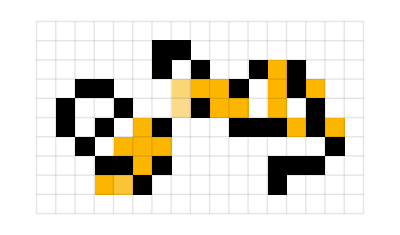

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[.1]]&[SortBy[Quiet[Select[{{"[◼]", "Data"}}["$LifeData"],#Class==="Oscillator"&&#Period==12&]],#Year&][[-2]]]
```

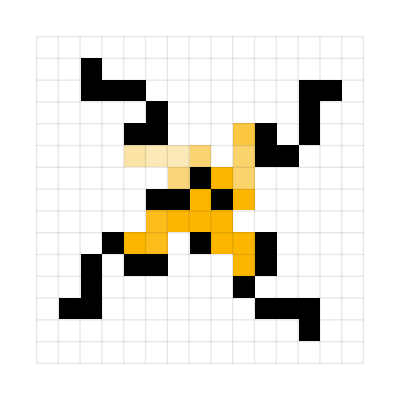
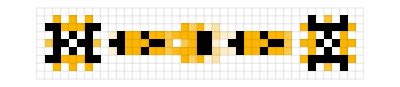
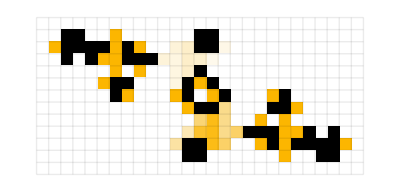
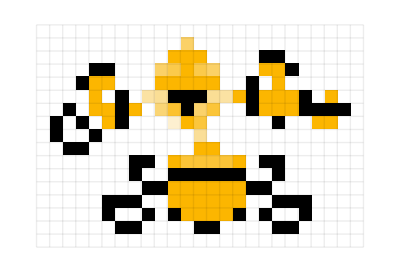
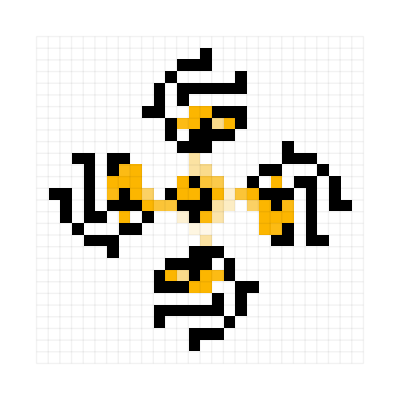
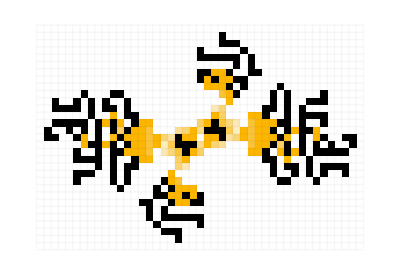
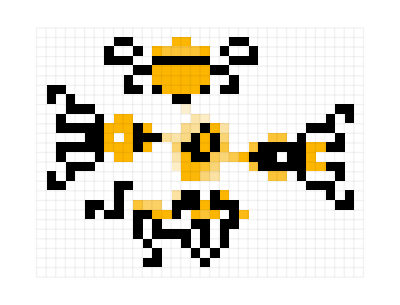
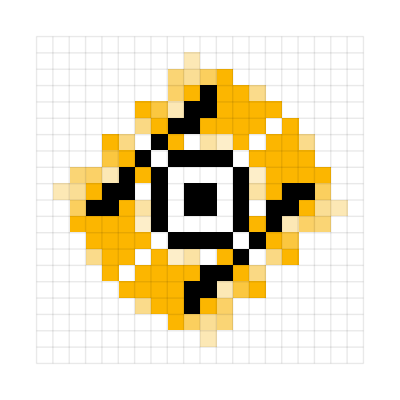
-Graphics-1972-Graphics-1984-Graphics-1989-Graphics-1994-Graphics-1995-Graphics-1995-Graphics-2004-Graphics-2009-Graphics-2015-Graphics-2019-Graphics-2021-Graphics-2022-Graphics-2022-Graphics-2023-Graphics-2023

```mathematica
Style[With[{data=Quiet[Append[Append[KeyDrop[Select[{{"[◼]", "Data"}}["$LifeData"],#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u={{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[{{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u={{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[{{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},Row[Values[Labeled[{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[(.7/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->18Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,GrayLevel[0.25]]]]&/@SortBy[data,#["Year"]&]],Spacer[4]]],LineSpacing->{1,1}]
```

```mathematica
data=Quiet[Append[Append[KeyDrop[Select[{{"[◼]", "Data"}}["$LifeData"],#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u={{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[{{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u={{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[{{"[◼]", "Data"}}["$LifeData"]["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]
```

<|Dinner table→<|Name→Dinner table,Year→1972,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Dinner_table,DataFiles→{dinnertable.cells,dinnertable.rle},MatrixData→SparseArray[Automatic,{13,13},0,{1,{{0,1,6,8,12,14,15,18,18,21,25,27,32,33},{{2},{2},{3},{4},{12},{13},{5},{12},{4},{5},{10},{12},{10},{11},{7},{5},{6},{8},{3},{7},{10},{2},{4},{5},{10},{2},{9},{1},{2},{10},{11},{12},{12}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→33|>,Carnival shuttle→<|Name→Carnival shuttle,Year→1984,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Carnival_shuttle,DataFiles→{carnivalshuttle.cells,carnivalshuttle.rle},MatrixData→SparseArray[Automatic,{7,38},0,{1,{{0,2,11,21,37,47,56,58},{{34},{38},{1},{2},{6},{7},{34},{35},{36},{37},{38},{2},{4},{6},{10},{13},{20},{21},{25},{28},{36},{2},{3},{5},{6},{9},{10},{14},{15},{20},{21},{24},{25},{29},{30},{35},{37},{2},{4},{6},{10},{13},{20},{21},{25},{28},{36},{1},{2},{6},{7},{34},{35},{36},{37},{38},{34},{38}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→58|>,Baker's dozen→<|Name→Baker's dozen,Year→1989,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Baker%27s_dozen,DataFiles→{bakersdozen.cells,bakersdozen.rle},MatrixData→SparseArray[Automatic,{11,23},0,{1,{{0,4,11,16,17,21,25,29,29,34,41,45},{{1},{2},{12},{13},{1},{2},{3},{4},{6},{12},{13},{1},{3},{6},{7},{8},{12},{5},{6},{11},{13},{5},{11},{14},{19},{12},{13},{18},{19},{16},{17},{18},{21},{23},{11},{12},{18},{20},{21},{22},{23},{11},{12},{22},{23}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→45|>,Crown→<|Name→Crown,Year→1994,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Crown,DataFiles→{crown.cells,crown.rle},MatrixData→SparseArray[Automatic,{14,23},0,{1,{{0,2,5,7,13,21,25,27,29,33,41,45,51,57,63},{{17},{18},{4},{5},{19},{3},{16},{6},{10},{11},{12},{16},{20},{2},{6},{11},{16},{20},{21},{22},{23},{1},{3},{6},{18},{1},{4},{2},{3},{7},{8},{17},{18},{7},{10},{11},{12},{13},{14},{15},{18},{8},{9},{16},{17},{5},{6},{7},{18},{19},{20},{5},{8},{10},{15},{17},{20},{6},{7},{12},{13},{18},{19}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→63|>,44P12.3→<|Name→44P12.3,Year→2009,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/44P12.3,DataFiles→{44p12.3.cells,44p12.3.rle},MatrixData→SparseArray[Automatic,{14,14},0,{1,{{0,1,3,5,6,11,14,22,30,33,38,39,41,43,44},{{8},{7},{8},{6},{7},{5},{4},{6},{7},{8},{9},{3},{5},{10},{2},{3},{5},{7},{8},{10},{13},{14},{1},{2},{5},{7},{8},{10},{12},{13},{5},{10},{12},{6},{7},{8},{9},{11},{10},{8},{9},{7},{8},{7}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→44|>,35P12.1→<|Name→35P12.1,Year→2015,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/35P12.1,DataFiles→{35p12.cells,35p12.rle},MatrixData→SparseArray[Automatic,{14,14},0,{1,{{0,2,3,6,7,9,10,10,14,19,23,30,32,34,35},{{4},{5},{4},{5},{6},{7},{7},{8},{9},{9},{4},{7},{11},{12},{2},{3},{4},{7},{12},{1},{6},{12},{14},{2},{3},{4},{6},{7},{13},{14},{4},{6},{4},{6},{5}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→35|>,Mold on fire-spitting→<|Name→Mold on fire-spitting,Year→2023,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Mold_on_fire-spitting,DataFiles→{moldonfirespitting.cells,moldonfirespitting.rle},MatrixData→SparseArray[Automatic,{8,15},0,{1,{{0,2,6,10,14,21,23,29,31},{{6},{7},{6},{8},{11},{13},{2},{3},{10},{13},{1},{4},{8},{14},{1},{3},{6},{10},{11},{12},{14},{2},{15},{3},{4},{6},{12},{13},{14},{5},{12}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→31|>,p12honeyfarmhassler→<|Name→p12honeyfarmhassler,Class→Oscillator,Year→2004,Period→12,Wiki→/wiki/Honey_farm_hasslers,DataFiles→{p12honeyfarmhassler.rle},MatrixData→SparseArray[Automatic,{24,32},0,{1,{{0,4,8,20,24,26,34,38,43,47,57,66,82,91,101,105,112,118,129,136,142,149,153,156,159},{{8},{9},{20},{21},{7},{10},{19},{22},{7},{8},{9},{12},{13},{14},{15},{16},{17},{20},{21},{22},{10},{11},{18},{19},{9},{20},{1},{2},{9},{10},{12},{17},{19},{20},{1},{3},{14},{15},{3},{4},{5},{31},{32},{2},{6},{30},{32},{2},{3},{4},{5},{6},{10},{17},{28},{29},{30},{5},{6},{10},{11},{12},{16},{18},{27},{31},{2},{3},{4},{5},{6},{10},{15},{16},{18},{23},{24},{25},{26},{27},{30},{31},{2},{6},{16},{17},{22},{23},{24},{26},{27},{3},{4},{5},{23},{24},{25},{26},{27},{30},{31},{1},{3},{27},{31},{1},{2},{8},{9},{28},{29},{30},{8},{15},{16},{18},{30},{32},{5},{6},{8},{14},{15},{16},{18},{19},{20},{31},{32},{5},{7},{8},{10},{11},{14},{20},{10},{12},{16},{17},{19},{20},{10},{12},{13},{14},{15},{17},{19},{11},{15},{17},{19},{12},{16},{18},{11},{12},{17}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→159|>,p12honeyfarmsparker→<|Name→p12honeyfarmsparker,Class→Oscillator,Year→2022,Period→12,Wiki→/wiki/Honey_farm_hasslers,DataFiles→{p12honeyfarmsparker.rle},MatrixData→SparseArray[Automatic,{25,37},0,{1,{{0,4,8,12,16,19,26,32,37,43,48,53,62,68,77,82,87,93,98,104,111,114,118,122,126,130},{{30},{31},{36},{37},{29},{32},{35},{37},{29},{30},{32},{35},{29},{32},{35},{37},{31},{36},{37},{1},{2},{7},{8},{25},{27},{28},{1},{3},{6},{9},{26},{27},{3},{6},{8},{9},{26},{1},{3},{6},{9},{27},{29},{1},{2},{7},{26},{30},{10},{11},{13},{26},{30},{11},{12},{17},{18},{19},{20},{21},{27},{29},{12},{17},{18},{20},{21},{26},{9},{11},{17},{18},{19},{20},{21},{26},{27},{8},{12},{25},{27},{28},{8},{12},{31},{36},{37},{9},{11},{29},{32},{35},{37},{12},{29},{30},{32},{35},{11},{12},{29},{32},{35},{37},{10},{11},{13},{30},{31},{36},{37},{1},{2},{7},{1},{3},{6},{9},{3},{6},{8},{9},{1},{3},{6},{9},{1},{2},{7},{8}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→130|>,p12honeyfarmhassler2→<|Name→p12honeyfarmhassler2,Class→Oscillator,Year→2023,Period→12,Wiki→/wiki/Honey_farm_hasslers,DataFiles→{p12honeyfarmhassler2.rle},MatrixData→SparseArray[Automatic,{22,26},0,{1,{{0,1,6,13,19,21,25,30,35,37,40,40,40,43,45,50,55,59,61,67,74,79,80},{{5},{1},{2},{3},{4},{6},{1},{2},{3},{5},{7},{13},{14},{6},{8},{13},{14},{20},{21},{7},{20},{6},{7},{18},{20},{6},{7},{14},{18},{19},{6},{7},{12},{13},{15},{12},{15},{12},{13},{14},{13},{14},{15},{12},{15},{12},{14},{15},{20},{21},{8},{9},{13},{20},{21},{7},{9},{20},{21},{7},{20},{6},{7},{13},{14},{19},{21},{13},{14},{20},{22},{24},{25},{26},{21},{23},{24},{25},{26},{22}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→80|>,p12honeyfarmhassler3→<|Name→p12honeyfarmhassler3,Class→Oscillator,Year→2022,Period→12,Wiki→/wiki/Honey_farm_hasslers,DataFiles→{p12honeyfarmhassler3.rle},MatrixData→SparseArray[Automatic,{14,19},0,{1,{{0,1,5,9,12,14,17,21,25,28,30,33,37,41,42},{{1},{1},{2},{3},{19},{4},{17},{18},{19},{3},{4},{16},{16},{17},{7},{8},{13},{6},{8},{12},{14},{6},{8},{12},{14},{7},{12},{13},{3},{4},{4},{16},{17},{1},{2},{3},{16},{1},{17},{18},{19},{19}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→42|>,p12lumpsofmuckhassler→<|Name→p12lumpsofmuckhassler,Class→Oscillator,Year→2019,Period→12,Wiki→/wiki/Lumps_of_muck_hasslers,DataFiles→{p12lumpsofmuckhassler.rle},MatrixData→SparseArray[Automatic,{17,40},0,{1,{{0,3,8,13,20,30,44,52,71,85,104,112,126,136,143,148,153,156},{{19},{20},{30},{19},{20},{29},{31},{36},{29},{31},{34},{35},{36},{6},{10},{11},{28},{29},{31},{33},{2},{5},{7},{9},{12},{26},{31},{34},{35},{36},{2},{3},{4},{5},{7},{9},{10},{12},{20},{29},{30},{31},{33},{36},{7},{12},{13},{19},{21},{25},{32},{33},{2},{3},{5},{6},{8},{9},{10},{11},{15},{18},{19},{21},{22},{25},{29},{33},{36},{39},{40},{1},{4},{6},{8},{10},{12},{19},{22},{29},{31},{33},{35},{37},{40},{1},{2},{5},{8},{12},{16},{19},{20},{22},{23},{26},{30},{31},{32},{33},{35},{36},{38},{39},{8},{9},{16},{20},{22},{28},{29},{34},{5},{8},{10},{11},{12},{21},{29},{31},{32},{34},{36},{37},{38},{39},{5},{6},{7},{10},{15},{29},{32},{34},{36},{39},{8},{10},{12},{13},{30},{31},{35},{5},{6},{7},{10},{12},{5},{10},{12},{21},{22},{11},{21},{22}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→156|>,p12blonktiehassler→<|Name→p12blonktiehassler,Class→Oscillator,Year→2021,Period→12,Wiki→/wiki/Blonk-tie_hasslers,DataFiles→{p12blonktiehassler.rle},MatrixData→SparseArray[Automatic,{39,42},0,{1,{{0,2,6,8,11,19,24,30,37,39,49,53,61,68,74,85,94,107,119,133,145,159,171,184,193,204,210,217,225,229,239,241,248,254,259,267,270,272,276,278},{{21},{22},{17},{18},{20},{22},{18},{20},{18},{20},{21},{17},{18},{20},{22},{24},{25},{27},{28},{16},{20},{21},{25},{27},{17},{18},{19},{23},{25},{27},{20},{21},{22},{23},{24},{25},{26},{17},{18},{16},{18},{20},{21},{23},{24},{25},{26},{27},{28},{16},{22},{24},{29},{17},{18},{19},{21},{23},{26},{27},{28},{19},{20},{25},{26},{32},{33},{37},{11},{31},{34},{36},{38},{41},{5},{10},{12},{31},{33},{34},{36},{38},{39},{40},{41},{5},{6},{7},{10},{12},{30},{31},{33},{36},{8},{10},{12},{13},{29},{32},{34},{35},{37},{38},{39},{40},{41},{5},{6},{7},{8},{10},{14},{29},{32},{35},{37},{39},{42},{5},{8},{10},{14},{18},{19},{21},{22},{23},{29},{35},{38},{41},{42},{7},{8},{10},{14},{18},{19},{24},{25},{29},{33},{35},{36},{1},{2},{5},{8},{14},{20},{21},{22},{24},{25},{29},{33},{35},{38},{1},{4},{6},{8},{11},{14},{29},{33},{35},{36},{37},{38},{2},{3},{4},{5},{6},{8},{9},{11},{14},{30},{31},{33},{35},{7},{10},{12},{13},{31},{33},{36},{37},{38},{2},{3},{4},{5},{7},{9},{10},{12},{31},{33},{38},{2},{5},{7},{9},{12},{32},{6},{10},{11},{17},{18},{23},{24},{15},{16},{17},{20},{22},{24},{25},{26},{14},{19},{21},{27},{15},{16},{17},{18},{19},{20},{22},{23},{25},{27},{25},{26},{17},{18},{19},{20},{21},{22},{23},{16},{18},{20},{24},{25},{26},{16},{18},{22},{23},{27},{15},{16},{18},{19},{21},{23},{25},{26},{22},{23},{25},{23},{25},{21},{23},{25},{26},{21},{22}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→278|>,new1→<|Name→new1,Class→Oscillator,Year→1995,Period→12,Wiki→/wiki/R-pentomino_hasslers,DataFiles→{p12rpentominohasslers.rle},MatrixData→SparseArray[…],InitialWeight→315|>,new2→<|Name→new2,Class→Oscillator,Year→1995,Period→12,Wiki→/wiki/R-pentomino_hasslers,DataFiles→{p12rpentominohasslers.rle},MatrixData→SparseArray[…],InitialWeight→315|>|>

```mathematica
SortBy[data,#["Year"]&][[8]]
```

<|Name→44P12.3,Year→2009,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/44P12.3,DataFiles→{44p12.3.cells,44p12.3.rle},MatrixData→SparseArray[Automatic,{14,14},0,{1,{{0,1,3,5,6,11,14,22,30,33,38,39,41,43,44},{{8},{7},{8},{6},{7},{5},{4},{6},{7},{8},{9},{3},{5},{10},{2},{3},{5},{7},{8},{10},{13},{14},{1},{2},{5},{7},{8},{10},{12},{13},{5},{10},{12},{6},{7},{8},{9},{11},{10},{8},{9},{7},{8},{7}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→44|>

```mathematica
{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]
```

<|Name→44P12.3,Year→2009,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/44P12.3,DataFiles→{44p12.3.cells,44p12.3.rle},MatrixData→SparseArray[Automatic,{14,14},0,{1,{{0,1,3,5,6,11,14,22,30,33,38,39,41,43,44},{{8},{7},{8},{6},{7},{5},{4},{6},{7},{8},{9},{3},{5},{10},{2},{3},{5},{7},{8},{10},{13},{14},{1},{2},{5},{7},{8},{10},{12},{13},{5},{10},{12},{6},{7},{8},{9},{11},{10},{8},{9},{7},{8},{7}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→44|>

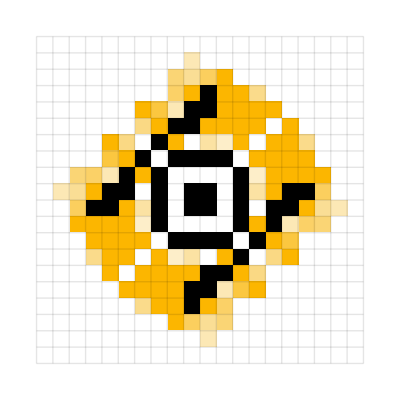

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[.1]]&[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]]
```

### Replacing mold on fire spitting with eye of sauron final

#### New

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[.1]]&[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]]
```

-Graphics-

```mathematica
GraphicsRow[Framed[#,FrameStyle->LightGray]&/@(GraphicsRow[{{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{{{"[◼]", "Data"}}["$LifeData"][#]["MatrixData"],0},24,ViewPoint->{0.9079906233946544,-2.941346308654788,1.4050035303835495}],{{"[◼]", "CellularAutomatonSpacetimePlot"}}["GameOfLife",{{{"[◼]", "Data"}}["$LifeData"][#]["MatrixData"],0},24, ImageSize->{Automatic, If[# ==="Carnival shuttle",  340, 120]}]},ImageSize->{Automatic,130}]&/@{"Carnival shuttle","44P12.3"}), Spacings->30]
```

-Graphics-

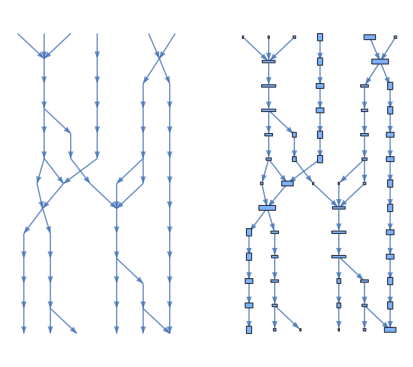
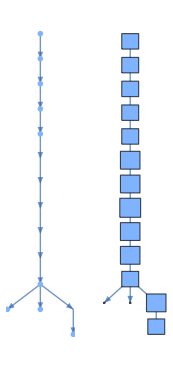

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 30, {{2-> 15, 3->15}, 3}]], FrameStyle->LightGray]&,Partition[Join[{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 350}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"], Automatic, ImageSize->{Automatic, 350}]},
{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 365}, PlotRangePadding->{0, 0}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#], Automatic, ImageSize->{Automatic, 365}, EdgeShapeFunction->"Arrow"]}&["44P12.3"]
], 2]], Spacer[25]]
```

### Code

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 30, {{2-> 15, 3->15}, 3}]], FrameStyle->LightGray]&,Partition[Join[{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 350}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"], Automatic, ImageSize->{Automatic, 350}]},
{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 365}, PlotRangePadding->{0, 0}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#], Automatic, ImageSize->{Automatic, 365}, EdgeShapeFunction->"Arrow"]}&["44P12.3"]
], 2]], Spacer[25]]
```

-Graphics--Graphics-

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 30, {{2-> 15, 3->15}, 3}]], FrameStyle->LightGray]&,Partition[Join[{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 350}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"]["Carnival shuttle"], Automatic, ImageSize->{Automatic, 350}]},
{{{"[◼]", "PatternsLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 365}, PlotRangePadding->{0, 0}],{{"[◼]", "BoundingBoxLayeredGraph"}}[{{"[◼]", "Data"}}["$LifeData"][#], Automatic, ImageSize->{Automatic, 365}, EdgeShapeFunction->"Arrow"]}&["44P12.3"]
], 2]], Spacer[25]]
```

-Graphics--Graphics-

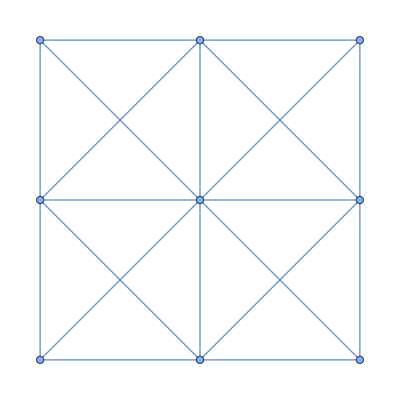

```mathematica
With[{vcs = Catenate[Table[{i, j}, {i, 1, 3}, {j, 1, 3}]]},
NearestNeighborGraph[vcs, {All, Sqrt[2]}]]
```

```mathematica
EuclideanDistance[{1, 1}, {2, 2}]
```

√2

```mathematica
2Sqrt[2] // N
```

2.82843

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[.1]]&[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]]
```

```mathematica
ArrayPlot/@(cas = CellularAutomaton["GameOfLife",{#["MatrixData"],0},12]&[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]
])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

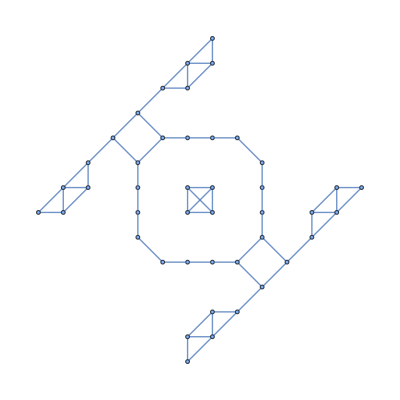
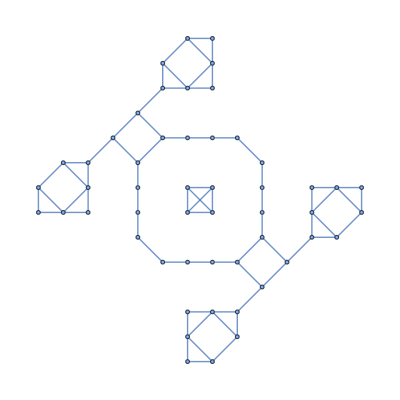
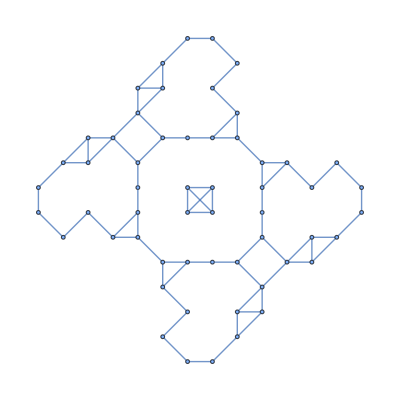
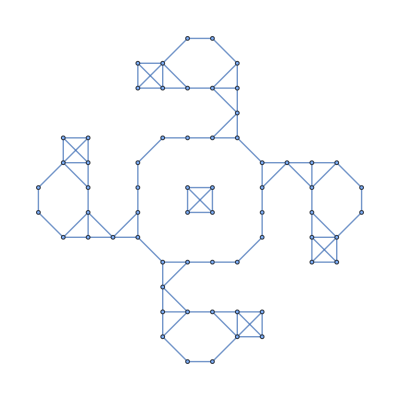
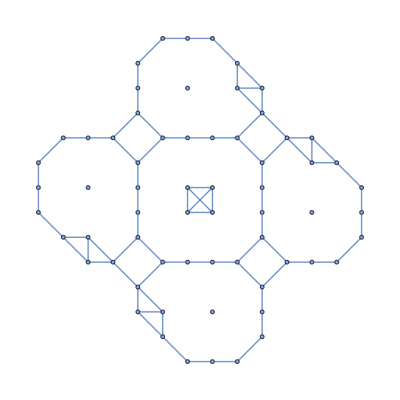
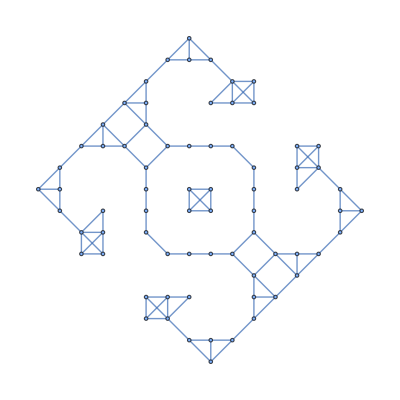
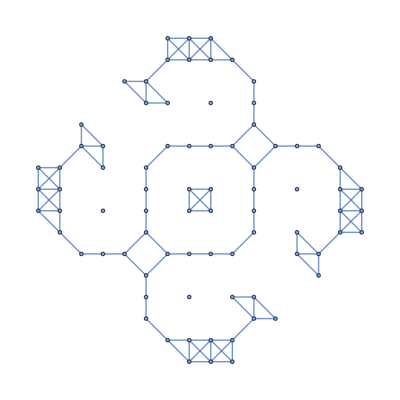
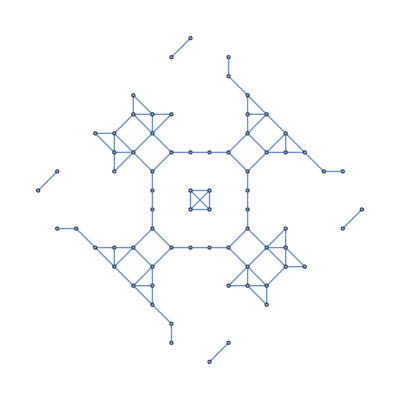
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NearestNeighborGraph[#,{All, Sqrt[2]}]&/@(Position[Transpose[
Reverse[Normal[#]]],1]&/@ cas)
```

### Trying to show duoplet sparks in causal graph

This doesn’t work because it rips apart other stuff

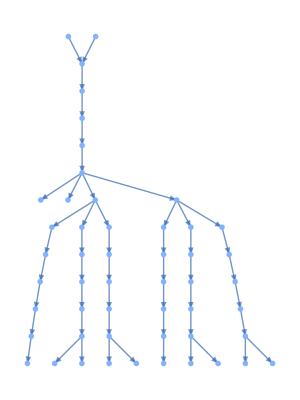

```mathematica
PatternsLayeredGraph[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]]
```

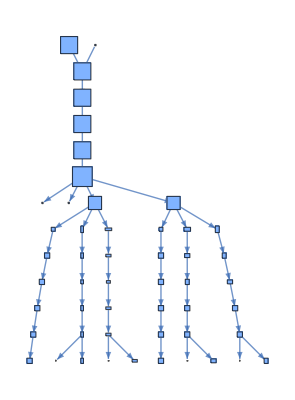

```mathematica
BoundingBoxLayeredGraph[{{"[◼]", "Data"}}["$LifeData"]["44P12.3"]]
```

```mathematica
{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#["MatrixData"],0},12,MeshStyle->Opacity[.1]]&[SortBy[Quiet[Select[{{"[◼]", "Data"}}["$LifeData"],#Class==="Oscillator"&&#Period==12&]],#Year&][[-2]]]
```

```mathematica
SortBy[Quiet[Select[{{"[◼]", "Data"}}["$LifeData"],#Class==="Oscillator"&&#Period==12&]],#Year&][[-2]]
```

<|Name→Mold on fire-spitting,Year→2023,Class→Oscillator,Period→12,Wiki→https://conwaylife.com/wiki/Mold_on_fire-spitting,DataFiles→{moldonfirespitting.cells,moldonfirespitting.rle},MatrixData→SparseArray[Automatic,{8,15},0,{1,{{0,2,6,10,14,21,23,29,31},{{6},{7},{6},{8},{11},{13},{2},{3},{10},{13},{1},{4},{8},{14},{1},{3},{6},{10},{11},{12},{14},{2},{15},{3},{4},{6},{12},{13},{14},{5},{12}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→31|>